L_p = 1.8E-14 m^2*s/kg at 4.°C

P_s = 1.9E-8 m/s at 4.°C

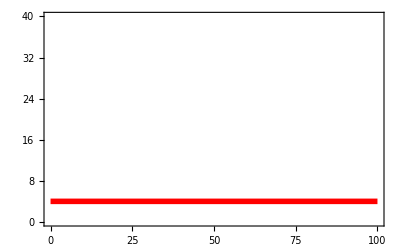
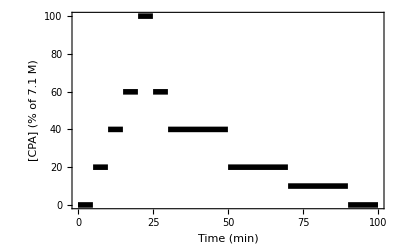
-Graphics--Graphics-CPA Exposure Profile 1

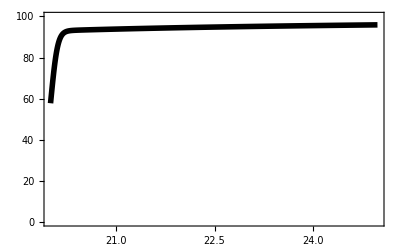
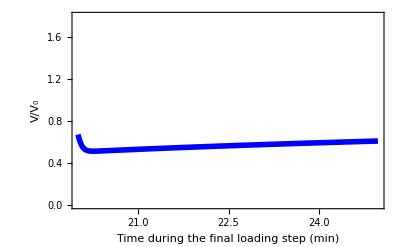
-Graphics--Graphics-Profile 1

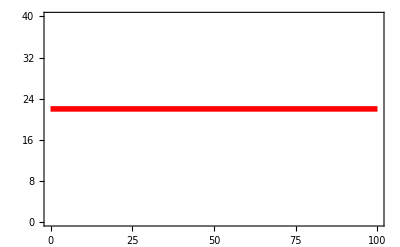
-Graphics--Graphics-CPA Exposure Profile 2

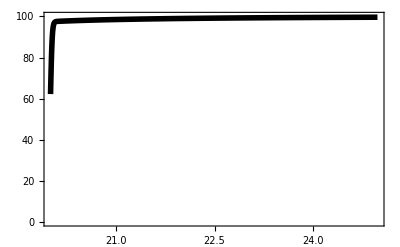
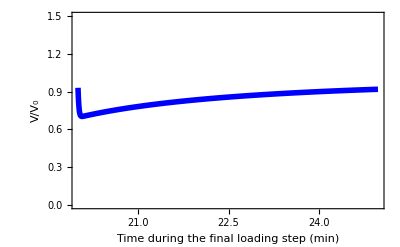
-Graphics--Graphics-Profile 2

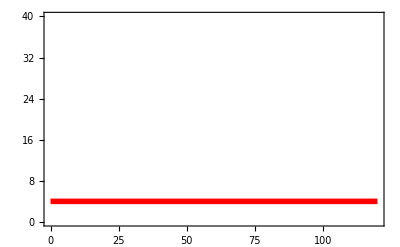
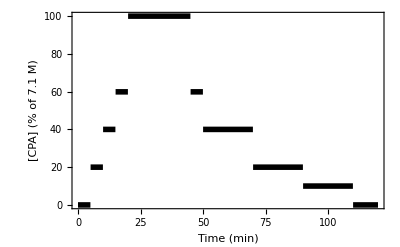
-Graphics--Graphics-CPA Exposure Profile 3

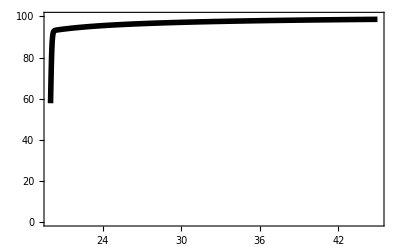
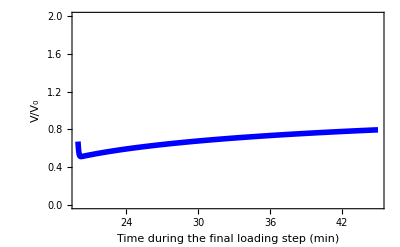
-Graphics--Graphics-Profile 3

-Graphics-

-Graphics-

```mathematica
(*Goals:
1. Plot Subscript[V, r](t)
2. Plot Subscript[C, i] (t)
3. Calculate min and max Subscript[V, r]
4. Calculate Subscript[C, i,Subscript[L, f]]
5. Compare to Program 4 (min V/V0 = 0.68, max V/V0 = 1.0, Subscript[C, i,Subscript[L, f]] = 99.66 %)
*)
(*Improvements from Program 4: 
1. Added equations to incorportate the inputted T in the Subscript[L, p] and Subscript[P, s] values
2. Changed the inputs to now include MW and ρ for the CPA(s), with MVCPA no longer an input (it gets calculated from these)
3. Fixed an error in plotting the shrink-swell during the final loading step
4. Relaxed the goals for FindMinimum and FindMaximum to prevent error messages which were occurring even though the result was good
5. Added the option of data export 
*)
(*Conclusions: 
1. Upon changing inputs and parameter values to be for my system, I got a realistic result of:
(1) for adhered ≠ 1 and Lp = 1.7E-13 and Ps = 6.8E-7 (same as in Program 3): 
a) for 5 min peak: min V/V0 = 0.72, max V/V0 = 1.29, Subscript[C, i,Subscript[L, f]] = 100.0 %
b) for 25 min peak: min V/V0 = 0.72, max V/V0 = 1.29, Subscript[C, i,Subscript[L, f]] = 100.0 %
(2) for adhered = 1 and Lp and Ps from my average of literature values (Subscript[L, p] = 1.8E-14 m^2*s/kg and Subscript[P, s] = 1.9E-8 m/s at 4°C):
a) for 5 min peak: min V/V0 = 0.51, max V/V0 = 1.62, Subscript[C, i,Subscript[L, f]] = 95.91 %
b) for 25 min peak: min V/V0 = 0.51, max V/V0 = 1.79, Subscript[C, i,Subscript[L, f]] = 98.61 %
*)

Clear["Global`*"]

(*inputs*)
profiles={
(*5 min peak, 4°C: *)
{{{0,t<5*60},{20,t<10*60},{40,t<15*60},{60,t<20*60},{100,t<25*60},{60,t<30*60},{40,t<50*60},{20,t<70*60},{10,t<90*60},{0,t<100*60}},4+273.15,5},
(*5 min peak, 22°C: *)
{{{0,t<5*60},{20,t<10*60},{40,t<15*60},{60,t<20*60},{100,t<25*60},{60,t<30*60},{40,t<50*60},{20,t<70*60},{10,t<90*60},{0,t<100*60}},22+273.15,5},
(*25 min peak, 4°C: *)
{{{0,t<5*60},{20,t<10*60},{40,t<15*60},{60,t<20*60},{100,t<45*60},{60,t<50*60},{40,t<70*60},{20,t<90*60},{10,t<110*60},{0,t<120*60}},4+273.15,5}
}; (*enter in the format: {surroudning CPA concentration as a function of time (c=f(t)), temperature (T), step number of the final loading step (locLf)}*)
MWCPA=71.34/1000; (*kg/mol, average molecular weight of CPA(s), compare to 71.34 g/mol for DEP, 78.14 for DMSO*)
ρCPA=1.085*1000; (*kg/m^3, average density of CPA(s), compare to 1.085 g/mL for DEP, compare to 1.1 for DMSO*)
Vb=.2*V0; (*osmotically inactive cell volume, compare to .2V0 for oocytes (Newton 1999)*)
adhered=1; (*enter 1 if cell is adherent (2D), enter ≠ 1 if cell is nonadherent (3D)*)
exportV=0; (*enter 1 if you want Subscript[V, r] = f(t) data to output as a table to copy-and-paste, enter ≠ 1 if not desired*)
exportC=0; (*enter 1 if you want Subscript[C, i] = f(t) data to output as a table to copy-and-paste, enter ≠ 1 if not desired*)

(*concentration inputs (comment out the input type (either osmolarity or osmolality) you do not want)*)
(*osmolarity inputs*)
inputsOsmolal=0; (*recommended to set at 0; if set at 1, the program will attempt to convert osmolality inputs*)
Cmax=7.09*1000; (*osmol/m^3 = mol/m^3 (true for CPA), max molarity of CPA surrounding the sample, compare to 7.09 M for DEP*)
C0=0*1000;(*osmol/m^3 = mol/m^3 (true for CPA), initial intracellular CPA molarity*)
Cn0=.323*1000;(*osmol/m^3, initial intracellular nonpenetrating osmolarity, compare to .323 for porcine myocardium*)
Cne=.332*1000;(*osmol/m^3, extracellular nonpenetrating osmolarity, compare to .332 for Celsior*)
(*(*osmolality inputs*)
inputsOsmolal=1; (*recommended to set at 1; any value other than 1: the program will not convert osmolality inputs to osmolarity*)
Mmax=2; (*osmol/kg, max osmolality of CPA surrounding the sample*)
M0=0; (*osmol/kg, initial intracellular CPA osmolality*)
Mn0=.3; (*osmol/kg, initial intracellular nonpenetrating osmolality, compare to .326 for porcine myocardium (Tranum-Jensen 1981)*)
Mne=.3; (*osmol/kg, extracellular nonpenetrating osmolality, compare to .335 for Celsior (Ostrozka-Cieslik 2009)*)*)

(*geometry inputs and calculations (comment out the geometry that you do not want)*)
(*(*inputs for a spherical geometry*)
Dcell=37/1000/1000; (*m, cell diameter, compare to 37 um for D22 hiPSC-CMs (my measurement using Cal+ImageJ: Subscript[size, avg]=1080 μm^2 (n=105)*)
(*equations for a spherical geometry*)
A0=π*Dcell^2; (*m^2, initial cell surface area, compare to 4.5E-6 for oocytes (Carbrey)*)
V0=π*Dcell^3/6; (*m^3, initial cell volume*)*)
(*inputs for an elliptical geometry*)
Lcell=110/1000/1000; (*m, length of cell, compare to 110 um for rat ventricular myocytes (Boyett 1991)*)
R1cell = 25/1000/1000; (*m, major radius of cell, compare to 25 um for rat ventricular myocytes (Boyett 1991)*)
RRatio=1/3; (*ratio of minor radius to major radius, compare to 1/3 for rat ventricular myocytes (Boyett 1991)*)
(*equations for an elliptical geomtery*)
R2cell=R1cell*RRatio; (*m, minor radius of cell*)
A0=π*Lcell*(R1cell+R2cell)+2*π*R1cell*R2cell; (*m^2, initial cell surface area*)
V0=π*Lcell*R1cell*R2cell/4; (*m^3, initial cell volume*)

(*key parameters*)
Tref=22+273.15; (*K, reference T, compare to 22 C in Wusteman 2001 and Wusteman 2002, compare to 25 C from Niu 2016*)
Lpref=10.8*10^-14; (*m^2*s/kg, reference Lp, DMSO in ECs at Tref (avg of Wusteman 2001, Wusteman 2002, and 1.226E-14 in Niu 2016)*)
ELp=68.3*1000; (*J/mol, activation energy Lp, DMSO in ECs (avg of Wusteman 2001, Wusteman 2002, and 40.15 in Niu 2016)*)
Psref=22*10^-8; (*m/s, reference Ps, DMSO in ECs at Tref (avg of Wusteman 2001, Wusteman 2002, and 5.925 in Niu 2016)*)
EPs=91.6*1000; (*J/mol, activation energy Ps, DMSO in ECs (avg of Wusteman 2001, Wusteman 2002, and 82.47 Niu 2016)*)

(*constants*)
Rgas=8.3145; (*J/mol/K = N*m/mol/K = kg*m^2/mol/K/s^2, gas constant*)

(*equations*)
If[adhered==1, (*if cell is adhered*)
A0=A0/2; (*assume half the cell membrane is exposed*)
]
MVCPA=MWCPA/ρCPA; (*m^3/mol, molar volume of CPA*)
Lp=Lpref*Exp[ELp/Rgas*(1/Tref-1/T)]; (*m^2*s/kg, hydraulic conductivity*)
Ps=Psref*Exp[EPs/Rgas*(1/Tref-1/T)]; (*m/s, CPA permeability*)

(*convert to osmolarity if necessary*)
If[inputsOsmolal==1,
Mw=55.55; (*mol water/kg water*)
Cw=55.346; (*mol water/L water*)
Cmax=1000*Mmax*(Cw-Mne-Mmax)/Mw; (*osmol/m^3 = mol/m^3 (true for CPA), max molarity of CPA surrounding the sample*)
Print["Max concentration of CPA surrounding the sample: "<>ToString[Mmax]<>" osmolal = "<>ToString[Cmax]<>" mM"];
C0=1000*M0*(Cw-Mn0-M0)/Mw;(*osmol/m^3 = mol/m^3 (true for CPA), initial intracellular CPA molarity*)
Print["Initial intracellular CPA concentration: "<>ToString[M0]<>" osmolal = "<>ToString[C0]<>" mM"];
Cn0=1000*Mn0*(Cw-Mn0-M0)/Mw; (*osmol/m^3, initial intracellular nonpenetrating osmolarity*)
Print["Initial intracellular nonpenetrating concentration: "<>ToString[Mn0]<>" osmolal = "<>ToString[Cn0]<>" mM"];
Cne=1000*Mne*(Cw-Mne)/Mw; (*osmol/m^3, extracellular nonpenetrating osmolarity*)
Print["Extracellular nonpenetrating concentration: "<>ToString[Mn0]<>" osmolal = "<>ToString[Cn0]<>" mM"];
];

(*initialization*)
If[exportV==1,VData={}];(*Subscript[V, r] vs t data points for each profile*)
If[exportC==1,CData={}]; (*Subscript[C, i] vs t data points for each profile*)
VPlots={};
CPlots={};
colors={Blue,Green,Black, Red,Purple,Orange,Brown,Yellow};
table={{"Profile","C_(e, SubscriptBox[L, f]) (M)","T (°C)","Δt_L_f (min)","t_tot (min)","Min V/V_0","Max V/V_0","C_(i, SubscriptBox[L, f]) (% of "<>ToString[Round[Cmax/1000,.1]]<>" M)"}};

(*execution*)
nProfiles=Length[profiles];
ttotmax=Max[profiles[[All,1]][[All,-1]][[All,2,2]]];
For[i=1,i<nProfiles+1,i++,
If[inputsOsmolal==1,(*if concentration unit is osmolality*)
Me=Piecewise[profiles[[i]][[1]]]*Mmax/100; (*mol/m^3 = mM, c=f(t)*)
Ce=1000*Me*(Cw-Mne-Me)/Mw; (*osmol/m^3 = mol/m^3 (true for CPA), extracellular CPA molarity*)
,(*if concentration unit is osmolarity*)
Ce=Piecewise[profiles[[i]][[1]]]*Cmax/100; (*mol/m^3 = mM, c=f(t)*)
];
T=profiles[[i]][[2]]; (*K, T=f(t)*)
If[i==1,
Print["L_p = "<>ToString[Round[10*MantissaExponent[Lp][[1]],.1]]<>"E"<>ToString[MantissaExponent[Lp][[2]]-1]<>" m^2*s/kg at "<>ToString[T-273.15]<>"°C"];
Print["P_s = "<>ToString[Round[10*MantissaExponent[Ps][[1]],.1]]<>"E"<>ToString[MantissaExponent[Ps][[2]]-1]<>" m/s at "<>ToString[T-273.15]<>"°C"];
];
locLf=profiles[[i]][[3]]; (*location of the final loading step*)
nSteps=Length[profiles[[i]][[1]]];(*number of c steps*)
ttot=Last[profiles[[i]][[1]]][[2,2]]; (*s, total simulation time*)
vnSol=NDSolve[{v'[t]==-Lp*A0*Rgas*T*(Cne+Ce-(Cn0*(V0-Vb))/(v[t]+n[t]*MVCPA)-n[t]/(v[t]+n[t]*MVCPA)),n'[t]==Ps*A0*(Ce-n[t]/(v[t]+n[t]*MVCPA)),v[0]==V0-Vb,n[0]==C0*(V0-Vb)},{v,n},{t,0,ttot},MaxStepSize->.1][[1]];
v[t_]:=Evaluate[v[t]/.vnSol[[1]]]; (*m^3, volume of intracellular water*)
n[t_]:=Evaluate[n[t]/.vnSol[[2]]];(*osmol = mol (true for CPA), amount of intracellular CPA*)
Vr[n_,v_]:=(v+MVCPA*n+Vb)/V0;(*ratio of cell volume to initial cell volume*)
Ci[n_,v_]:=n/(v+MVCPA*n);(*mol/m^3, intracellular [CPA]*)
(*initialization*)
Vmins={}; (*list of Vmin for each step*)
Vmaxs={}; (*list of Vmax for each step*)
tPriorSteps=0; (*s, time of all prior steps*)
For[j=1,j<nSteps+1,j++,
tCurrentStep=profiles[[i]][[1]][[j]][[2,2]]; (*s, time until the end of the current step*)
If[j≤locLf,(*if this is a loading step*)
AppendTo[Vmins,FindMinimum[{Vr[n[t],v[t]],tPriorSteps<t<tCurrentStep},t,AccuracyGoal->1,PrecisionGoal->1][[1]]];
If[j==locLf, (*if this is the final loading step*)
tL=tPriorSteps; (*s, time at beginning of final loading step*)
DtL=tCurrentStep-tPriorSteps; (*s, duration of the final loading step*)
tLf=tCurrentStep-1; (*s, time at the end of the final loading step*)
t=tLf;
CeLf=Ce;
CiLf=Ci[n[t],v[t]];
Clear[t];
];
,(*if this is an unloading step*)
AppendTo[Vmaxs,FindMaximum[{Vr[n[t],v[t]],tPriorSteps<t<tCurrentStep},t,AccuracyGoal->1,PrecisionGoal->1][[1]]];
];
tPriorSteps=tCurrentStep;
];
Vmin=If[Length[Vmins]>0,Min[Vmins],Min[{Vr[n[0],v[0]],Vr[n[ttot],v[ttot]]}]];
Vmax=If[Length[Vmaxs]>0,Max[Vmaxs],Max[{Vr[n[0],v[0]],Vr[n[ttot],v[ttot]]}]];
Ce=Ce/.t->t*60; (*for plotting in min*)
Print[Labeled[Overlay[{Plot[T-273.15,{t,0,ttot/60},PlotStyle->{Red,Thickness[.01]},ImagePadding->{{45,45},{45,5}},PlotRange->{0,40},Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Red},FrameLabel->{{None,"T (°C)"},{None,None}}],Plot[Floor[Ce*100/Cmax,.1],{t,0,ttot/60},PlotStyle->{Black,Thickness[.01]},ImagePadding->{{45,45},{45,5}},PlotRange->{0,100},Frame->{True,True,False,False},FrameStyle->{Automatic,Black,Automatic,Automatic},FrameLabel->{{If[inputsOsmolal==1,"[CPA] (% of "<>ToString[NumberForm[Mmax,2]]<>" molal)","[CPA] (% of "<>ToString[NumberForm[Cmax/1000,2]]<>" M)"],None},{"Time (min)",None}}]}],"CPA Exposure Profile "<>ToString[i],Top]];
If[i<nProfiles,(*if this is not the last profile*)
AppendTo[VPlots,Plot[If[t<ttot/60,Vr[n[t*60],v[t*60]]],{t,0,ttotmax/60},PlotRange->{{0,ttotmax/60},{0,Ceiling[1.1*Vmax,.1]}},AxesLabel->{"t (min)","V/V_0"},PlotStyle->colors[[i]]]];
AppendTo[CPlots,Plot[If[t<ttot/60,100*Ci[n[t*60],v[t*60]]/Cmax],{t,0,ttotmax/60},PlotRange->{{0,ttotmax/60},{0,100}},AxesLabel->{"t (min)",If[inputsOsmolal==1,"[CPA] (% of "<>ToString[NumberForm[Mmax,2]]<>" molal)","[CPA] (% of "<>ToString[NumberForm[Cmax/1000,2]]<>" M)"],None},PlotStyle->colors[[i]]]];
,(*if this is the last profile*)
AppendTo[VPlots,Plot[If[t<ttot/60,Vr[n[t*60],v[t*60]]],{t,0,ttotmax/60},PlotRange->{0,Ceiling[1.1*Vmax,.1]},AxesLabel->{"t (min)","V/V_0"},PlotStyle->colors[[i]],PlotLegends->Placed[LineLegend[colors,Range[nProfiles],LegendLabel->"Profile",LegendFunction->Framed],{1,.6}]]];
AppendTo[CPlots,Plot[If[t<ttot/60,100*Ci[n[t*60],v[t*60]]/Cmax],{t,0,ttotmax/60},PlotRange->{0,100},AxesLabel->{"t (min)",If[inputsOsmolal==1,"[CPA] (% of "<>ToString[NumberForm[Mmax,2]]<>" molal)","[CPA] (% of "<>ToString[NumberForm[Cmax/1000,2]]<>" M)"],None},PlotStyle->colors[[i]],PlotLegends->Placed[LineLegend[colors,Range[nProfiles],LegendLabel->"Profile",LegendFunction->Framed],{1,.6}]]];
];
If[exportV==1,AppendTo[VData,Cases[VPlots[[i]],Line[VData_]:>VData,-4,1][[1]]]];
If[exportC==1,AppendTo[CData,Cases[CPlots[[i]],Line[CData_]:>CData,-4,1][[1]]]];
Print[Labeled[Overlay[{Plot[100*Ci[n[t*60],v[t*60]]/Cmax,{t,tL/60,tLf/60},PlotStyle->{Black,Thickness[.01]},ImagePadding->{{45,45},{45,5}},PlotRange->{0,100},Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Black},FrameLabel->{{None,If[inputsOsmolal==1,"[CPA] (% of "<>ToString[NumberForm[Mmax,2]]<>" molal)","[CPA] (% of "<>ToString[NumberForm[Cmax/1000,2]]<>" M)"]},{None,None}}],Plot[Vr[n[t*60],v[t*60]],{t,tL/60,tLf/60},PlotStyle->{Blue,Thickness[.01]},ImagePadding->{{45,45},{45,5}},PlotRange->{0,Ceiling[1.1*Vmax,.1]},Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic},FrameLabel->{{"V/V_0",None},{"Time during the final loading step (min)",None}}]}],"Profile "<>ToString[i],Top]];
AppendTo[table,{i,Round[CeLf/1000,.1],Round[T-273.15,.1],DtL/60,ttot/60,Round[Vmin,.01],Round[Vmax,.01],Round[100*CiLf/CeLf,.01]}];
Clear[v,n];
]; (*end of i loop*)
Show[VPlots]
Show[CPlots]
Dataset[AssociationThread[First@table->#]&/@Rest@table]
For[i=1,i<nProfiles+1,i++,
If[exportV==1,
Print["V_r = f(t) for Profile "<>ToString[i]<>":"];
Print[VData[[i]]//TableForm];
];
If[exportC==1,
Print["C_i = f(t) for Profile "<>ToString[i]<>":"];
Print[CData[[i]]//TableForm];
];
];
```